It looks as if variable names do not survive the import process.

The variables are:

dependence

dependence measure id

instance id

num samples

relation id

x noise std

y noise std

```mathematica
rand=Import["00000_random_x000_y000.mat"];
```

```mathematica
Dimensions[rand]
```

{7,1290240,1}

We need to flatten to get rid of that last dimension.

```mathematica
randF=Flatten/@rand;
```

```mathematica
randF[[{1,2,3,4,5,6,7},6]]
```

{0.97095,4.,1.,5.,0.,0.,0.}

```mathematica
foo=randF[[2]];
```

```mathematica
Take[foo,5]
```

{4.,5.,1.,2.,3.}

```mathematica
xp=Transpose[randF];
```

Gives the (numericized) maximum likelihood estimate of the cumulative probability of each unique member of the list l in sorted order. So, the list {3,2,3,3,3,3,2,1,3,3} would return {0.1,0.3,1.0} since the individiual entries (in order) have probabilities {0.1, 0.2,and 0.7}

```mathematica
cdf[l_List]:=N[Accumulate[Map[#[[2]]/Length[l]&,Sort[Tally[l],#1[[1]]<#2[[1]]&]]]]
```

```mathematica
cdf[{3,2,3,3,3,3,2,1,3,3}]
```

{0.1,0.3,1.}

```mathematica
pairWiseDistances[l_List]:=Map[l[[#+1]]-l[[#]]&,Range[Length[l]-1]]
```

```mathematica
nearestNeighborDistances[unsorted_List]:=With[{l=Sort[unsorted]},Which[
Length[l]==1,{0},
Length[l]==2,With[{d=l[[2]]-l[[1]]},{d,d}],
True,With[{pwd=pairWiseDistances[l]},
Flatten[{pwd[[1]],Map[Min[pwd[[#]],pwd[[#+1]]]&,Range[Length[pwd]-1]],pwd[[Length[pwd]]]}]
]
]]
```

```mathematica
nearestNeighborDistances[{1}]
```

{0}

```mathematica
nearestNeighborDistances[{1,2}]
```

{1,1}

```mathematica
nearestNeighborDistances[{1,2,8}]
```

{1,1,6}

```mathematica
nearestNeighborDistances[{1,2,2,8}]
```

{1,0,0,6}

Display the dependence measures with a specified number of bins (or dependence measure id) and sample size as a column containing: the sorted values and the number of occurrences for each, the cumulative probabilities of each value, and the same information displayed as a histogram.

```mathematica
analyzeSampleBinCombo[nSamples_,nBins_,xp_List]:=With[{deps=#[[1]]&/@Select[xp,#[[2]]==nBins && #[[4]]==nSamples&]},
Column[{Sort[Tally[deps],#1[[1]]<#2[[1]]&],
cdf[deps],nearestNeighborDistances[Union[deps]],Histogram[deps,100,"Probability",ImageSize->Large]},Frame->All]]
```

```mathematica
primesLessThanOrEqualTo[n_]:=Flatten[Which[
n<2,{},
PrimeQ[n],{n,primesLessThanOrEqualTo[NextPrime[n,-1]]},
True,primesLessThanOrEqualTo[NextPrime[n,-1]]
]]
```

```mathematica
primesLessThanOrEqualTo[10]
```

{7,5,3,2}

```mathematica
primesLessThanOrEqualTo[11]
```

{11,7,5,3,2}

```mathematica
allHistograms[nSamples_,xp_List]:=
With[{correctSampXP=Select[xp,#[[4]]==nSamples&]},
Column[
Map[Function[nBins,
Histogram[#[[1]]&/@Select[correctSampXP,#[[2]]==nBins&],Automatic,"Probability",PlotLabel->ToString[nSamples]~~" samples & "~~ToString[nBins]~~" bins",ImageSize->Medium]],
With[{primes=primesLessThanOrEqualTo[nSamples]},Complement[Range[4,nSamples],primes]]],Frame->All]]
```

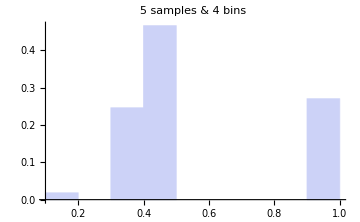

```mathematica
allHistograms[5,xp]
```

```mathematica
allNonMICHistograms[nSamples_,xp_List]:=
With[{correctSampXP=Select[xp,#[[4]]==nSamples&]},
Column[
Map[Function[nBins,
Histogram[#[[1]]&/@Select[correctSampXP,#[[2]]==nBins&],Automatic,"Probability",PlotLabel->ToString[nSamples]~~" samples & method id="~~ToString[nBins],ImageSize->Medium]],
{1.,2.,3.}],Frame->All]]
```

## 5 samples

### MIC

For our first trick, lets look at the distribution of 5 samples. This will only support 4 bins, so this is really 5 samples 4 bins.

```mathematica
samp5=Select[xp,#[[2]]==4. &&#[[4]]==5.&];
```

```mathematica
samp5dep=#[[1]]&/@samp5;
```

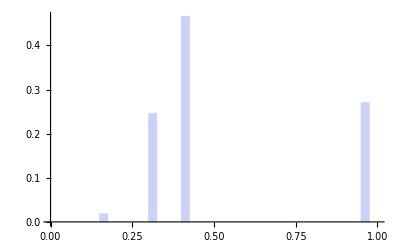

```mathematica
Histogram[samp5dep,40,"Probability"]
```

```mathematica
Union[samp5dep]
```

{0.17095,0.32192,0.41997,0.97095}

For 5 samples, there is a 27% chance of a 0.97 mic with random data and a 73% chance of a mic below 0.47.

### Non-MIC

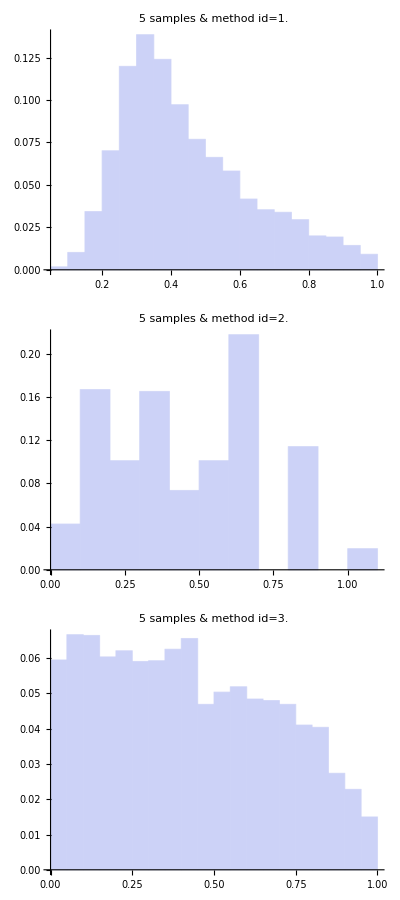

```mathematica
allNonMICHistograms[5,xp]
```

## 6 samples

### MIC

6 samples has two valid bin widths. Since that is still a managable number, I'll treat them separately.

```mathematica
samp6bin4=Select[xp,#[[2]]==4. && #[[4]]==6.&];
```

```mathematica
samp6bin4dep=#[[1]]&/@samp6bin4;
```

```mathematica
Union[samp6bin4dep]
```

{0.19087,0.45914,1.}

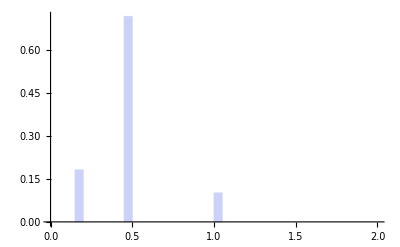

```mathematica
Histogram[samp6bin4dep,40,"Probability"]
```

With 6 samples and 4 bins there is a 90% chance of having a value below 0.5.

```mathematica
samp6bin6=Select[xp,#[[2]]==6. && #[[4]]==6.&];
```

```mathematica
samp6bin6dep=#[[1]]&/@samp6bin6;
```

```mathematica
Union[samp6bin6dep]
```

{0.33333,0.54085,0.66666,0.91829,1.}

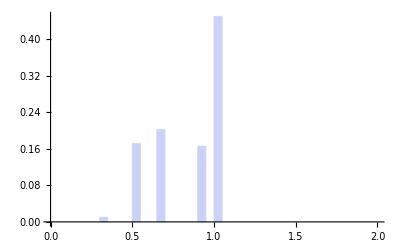

```mathematica
Histogram[samp6bin6dep,40,"Probability"]
```

However, with 6 bins, there is a 99% chance of having a value above 0.5. In fact, there is only a 55% chance of having a value at 0.918 or below. All others are 1.

### Non-mic

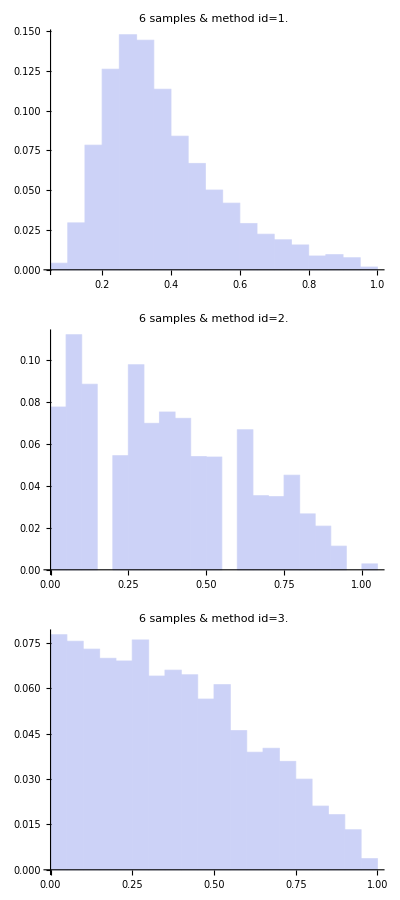

```mathematica
allNonMICHistograms[6,xp]
```

## 7 samples

### MIC

7 samples has two valid bin widths. Since that is still a managable number, I'll treat them separately.

```mathematica
samp7bin4=Select[xp,#[[2]]==4. && #[[4]]==7.&];
```

```mathematica
samp7bin4dep=#[[1]]&/@samp7bin4;
```

```mathematica
Union[samp7bin4dep]
```

{0.12808,0.19811,0.29169,0.46956,0.52164,0.98522}

```mathematica
cdf[samp7bin4dep]
```

{0.00889757,0.131076,0.439887,0.70855,0.924262,1.}

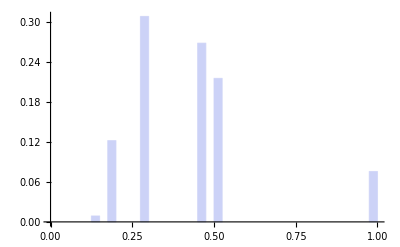

```mathematica
Histogram[samp7bin4dep,40,"Probability"]
```

With 7 samples and 4 bins there is a 92% chance of having a value below 0.521. Interestingly, for scores below 0.5, now there is only a 71% chance as opposed to the 90% chance there was with 4 bins and 6 samples. This implies that mic scores are not comparable across number of samples.

```mathematica
samp7bin6=Select[xp,#[[2]]==6. && #[[4]]==7.&];
```

```mathematica
samp7bin6dep=#[[1]]&/@samp7bin6;
```

```mathematica
Sort[Tally[samp7bin6dep],#1[[1]]<#2[[1]]&]
```

{{0.30595,23},{0.41379,143},{0.46956,77},{0.52164,213},{0.59167,1228},{0.69951,655},{0.86312,699},{0.98522,1570}}

```mathematica
cdf[samp7bin6dep]
```

{0.00499132,0.0360243,0.0527344,0.0989583,0.365451,0.507595,0.659288,1.}

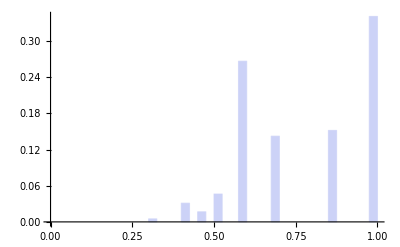

```mathematica
Histogram[samp7bin6dep,40,"Probability"]
```

When we increase the number of bins, the situation suddenly looks a lot worse again. Only 5% are under 0.5 and the highest threshold that is not 1 (or really, not 0.98), only gets 66% marked as random. This is still an improvement over 55% for 6 samples.

### Non-mic

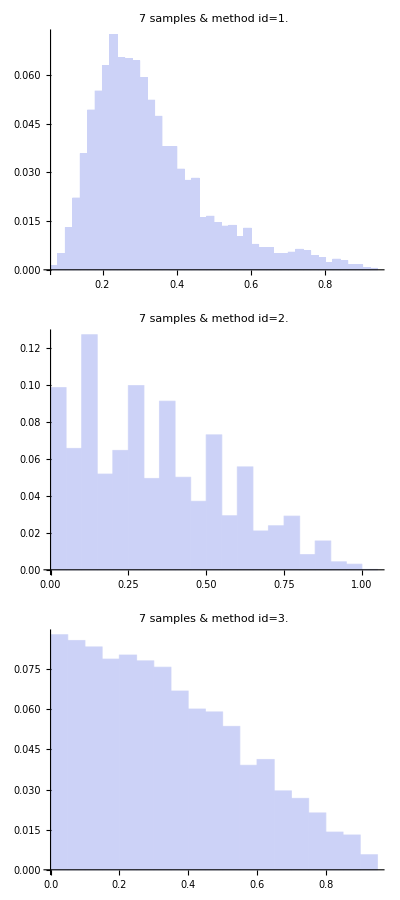

```mathematica
allNonMICHistograms[7,xp]
```

## 8 samples

### MIC

8 samples has three valid numbers of bins. That is getting unwieldly, but I'll still treat them separately.

Note that with 6 bins, I have quite a number of bins with 1 sample, indicating that the sample size of 4608 instances isn't sufficient to get all the possible MICs.

#### 4 bins

```mathematica
samp8bin4=Select[xp,#[[2]]==4. && #[[4]]==8.&];
```

```mathematica
samp8bin4dep=#[[1]]&/@samp8bin4;
```

```mathematica
Union[samp8bin4dep]
```

{0.13792,0.18872,0.31127,0.54879,1.}

```mathematica
cdf[samp8bin4dep]
```

{0.102865,0.132595,0.664497,0.972873,1.}

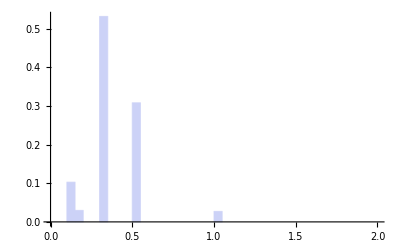

```mathematica
Histogram[samp8bin4dep,40,"Probability"]
```

With 8 samples and 4 bins there is a 97% chance of having a value below 0.549. Again that threshold has gone up. Interestingly, for scores below 0.5, now there is only a 66% chance as opposed to the 90% chance there was with 4 bins and 6 samples.

#### 6 bins

```mathematica
samp8bin6=Select[xp,#[[2]]==6. && #[[4]]==8.&];
```

```mathematica
samp8bin6dep=#[[1]]&/@samp8bin6;
```

```mathematica
Sort[Tally[samp8bin6dep],#1[[1]]<#2[[1]]&]
```

{{0.26571,1},{0.29356,4},{0.31127,12},{0.34436,10},{0.36007,1},{0.39315,332},{0.46691,16},{0.5,398},{0.54879,301},{0.59436,512},{0.61007,184},{0.65563,925},{0.75,440},{0.81127,457},{0.95443,129},{1.,886}}

```mathematica
cdf[samp8bin6dep]
```

{0.000217014,0.00108507,0.00368924,0.00585938,0.00607639,0.078125,0.0815972,0.167969,0.23329,0.344401,0.384332,0.585069,0.680556,0.779731,0.807726,1.}

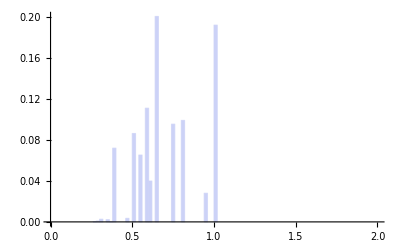

```mathematica
Histogram[samp8bin6dep,100,"Probability"]
```

For 6 bins, 81% lie at or below a score of 0.954. But a full 19% have a score of 1.

#### 8 bins

```mathematica
samp8bin8=Select[xp,#[[2]]==8. && #[[4]]==8.&];
```

```mathematica
samp8bin8dep=#[[1]]&/@samp8bin8;
```

```mathematica
Sort[Tally[samp8bin8dep],#1[[1]]<#2[[1]]&]
```

{{0.39315,6},{0.40563,12},{0.5,59},{0.59436,80},{0.61007,19},{0.65563,340},{0.70443,420},{0.75,439},{0.81127,578},{1.,2655}}

```mathematica
cdf[samp8bin8dep]
```

{0.00130208,0.00390625,0.0167101,0.0340712,0.0381944,0.111979,0.203125,0.298394,0.423828,1.}

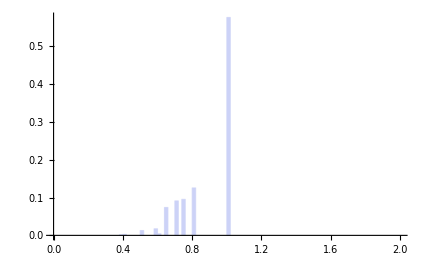

```mathematica
Histogram[samp8bin8dep,100,"Probability"]
```

For 8 bins, 58% have a score of 1. 48% have a score less than that (the top non-unity score being 0.811)

### Non-mic

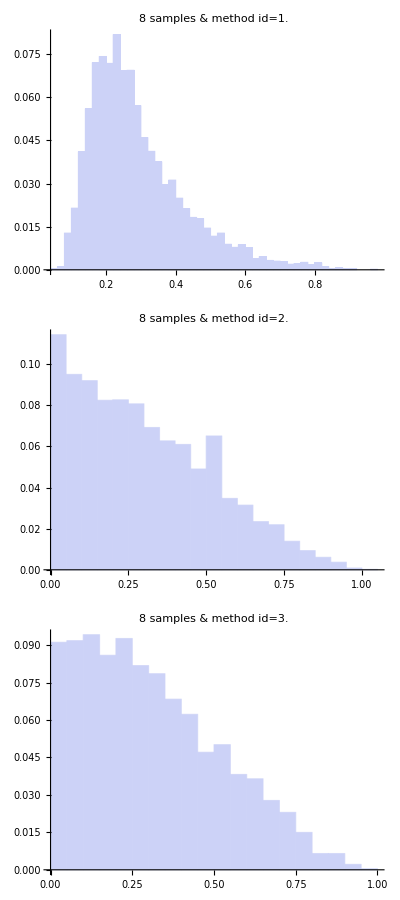

```mathematica
allNonMICHistograms[8,xp]
```

## 9 samples

### MIC

9 samples has four valid numbers of bins. I think treating them separately is still good for understanding the data.

#### 4 bins

```mathematica
samp9bin4=Select[xp,#[[2]]==4. && #[[4]]==9.&];
```

```mathematica
samp9bin4dep=#[[1]]&/@samp9bin4;
```

```mathematica
Sort[Tally[samp9bin4dep],#1[[1]]<#2[[1]]&]
```

{{0.10218,35},{0.14269,374},{0.22478,795},{0.22943,236},{0.31976,1131},{0.37887,1073},{0.55772,471},{0.59,400},{0.99107,93}}

```mathematica
cdf[samp9bin4dep]
```

{0.00759549,0.0887587,0.261285,0.3125,0.557943,0.790799,0.893012,0.979818,1.}

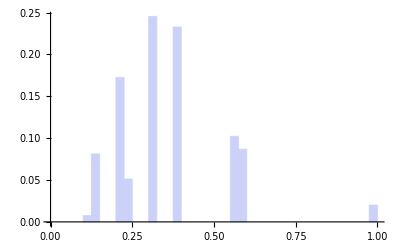

```mathematica
Histogram[samp9bin4dep,40,"Probability"]
```

The chance of having a value lower than the second highest value only rises about 1% from 8 samples (98% rather than 97%), and that second-highest value goes from 0.54879 to 0.59.

##### Values appearing in pairs

It is interesting that many of the values seem to be appearing in pairs. The calculation below shows that the first 8 values are paired with one another in groups of two.

```mathematica
Union[samp9bin4dep]
```

{0.10218,0.14269,0.22478,0.22943,0.31976,0.37887,0.55772,0.59,0.99107}

```mathematica
nearestNeighborDistances[Union[samp9bin4dep]]
```

{0.04051,0.04051,0.00465001,0.00465001,0.05911,0.05911,0.03228,0.03228,0.40107}

Only the first two are paired in the 8 sample 4 bin instances

```mathematica
nearestNeighborDistances[Union[samp8bin4dep]]
```

{0.0508,0.0508,0.12255,0.23752,0.45121}

The 7 sample 4 bin instances have two pairs

```mathematica
nearestNeighborDistances[Union[samp7bin4dep]]
```

{0.07003,0.07003,0.09358,0.05208,0.05208,0.46358}

The 6 sample 4 bin instances are only in pairs (but not surprising since there are only 3 values that occur).

```mathematica
nearestNeighborDistances[Union[samp6bin4dep]]
```

{0.26827,0.26827,0.54086}

For 5 samples, it is the middle two values that are paired.

```mathematica
nearestNeighborDistances[Union[samp5dep]]
```

{0.15097,0.09805,0.09805,0.55098}

#### 6 bins

```mathematica
samp9bin6=Select[xp,#[[2]]==6. && #[[4]]==9.&];
```

```mathematica
samp9bin6dep=#[[1]]&/@samp9bin6;
```

```mathematica
Sort[Tally[samp9bin6dep],#1[[1]]<#2[[1]]&]
```

{{0.24053,3},{0.30609,3},{0.3244,50},{0.36778,7},{0.37887,188},{0.40828,31},{0.45165,392},{0.4581,525},{0.54663,313},{0.55772,196},{0.59,315},{0.6305,553},{0.68497,926},{0.76885,242},{0.91829,269},{0.99107,595}}

```mathematica
cdf[samp9bin6dep]
```

{0.000651042,0.00130208,0.0121528,0.0136719,0.0544705,0.0611979,0.146267,0.2602,0.328125,0.37066,0.439019,0.559028,0.759983,0.8125,0.870877,1.}

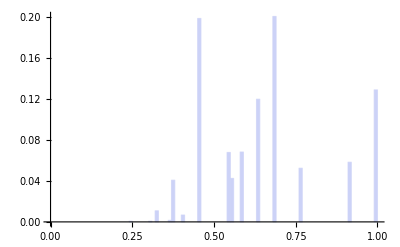

```mathematica
Histogram[samp9bin6dep,100,"Probability"]
```

With 6 bins, we are up to 87% for the second highest score (at score 0.918) (which thresholds are both improved from 81% and 0.954 with 8 samples). 13% have the highest score of 0.99107.

#### 8 bins

```mathematica
samp9bin8=Select[xp,#[[2]]==8. && #[[4]]==9.&];
```

```mathematica
samp9bin8dep=#[[1]]&/@samp9bin8;
```

```mathematica
Sort[Tally[samp9bin8dep],#1[[1]]<#2[[1]]&]
```

{{0.37887,4},{0.45165,40},{0.4581,24},{0.46275,40},{0.54663,117},{0.59,43},{0.61219,11},{0.6305,268},{0.68497,706},{0.69607,276},{0.7642,276},{0.76885,727},{0.91829,74},{0.99107,2002}}

```mathematica
cdf[samp9bin8dep]
```

{0.000868056,0.00954861,0.0147569,0.0234375,0.0488281,0.0581597,0.0605469,0.118707,0.271918,0.331814,0.39171,0.549479,0.565538,1.}

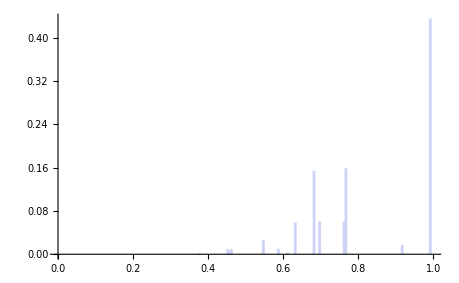

```mathematica
Histogram[samp9bin8dep,200,"Probability"]
```

With 9 samples and 8 bins, the situation is still quite bleak. 43% of the samples have the highest value (0.991). This is down from 58% for the 8 sample case.

#### 9 bins

```mathematica
samp9bin9=Select[xp,#[[2]]==9. && #[[4]]==9.&];
```

```mathematica
samp9bin9dep=#[[1]]&/@samp9bin9;
```

```mathematica
Sort[Tally[samp9bin9dep],#1[[1]]<#2[[1]]&]
```

{{0.37887,2},{0.38625,1},{0.43917,1},{0.45165,25},{0.4581,4},{0.46275,15},{0.46653,17},{0.49209,15},{0.51945,8},{0.54663,93},{0.57938,40},{0.59,42},{0.61219,11},{0.61374,5},{0.6305,268},{0.68497,701},{0.69607,271},{0.7642,275},{0.76885,701},{0.7725,37},{0.91829,74},{0.99107,1988},{1.,14}}

```mathematica
cdf[samp9bin9dep]
```

{0.000434028,0.000651042,0.000868056,0.0062934,0.00716146,0.0104167,0.0141059,0.0173611,0.0190972,0.0392795,0.0479601,0.0570747,0.0594618,0.0605469,0.118707,0.270833,0.329644,0.389323,0.54145,0.549479,0.565538,0.996962,1.}

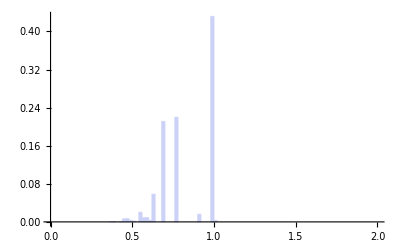

```mathematica
Histogram[samp9bin9dep,100,"Probability"]
```

For the 9 bin case with 9 samples, things look, on the one hand, slightly better than the 8 bin case. Much more than 99% of the samples have values less than the maximum. The maximum here is 1. But that number is a bit deceiving because the second highest score is 0.991 (very close to 1) and 57% are less than that. The third highest score is 0.918 and 55% are rejected by that criterion.

### Non-mic

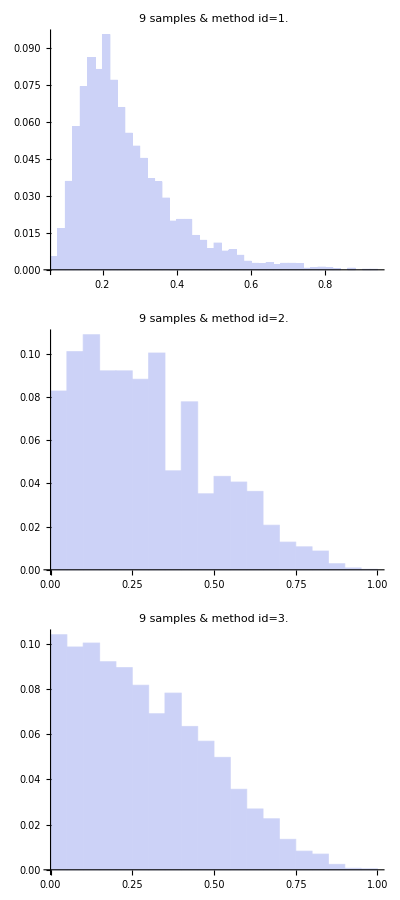

```mathematica
allNonMICHistograms[9,xp]
```

## 10 samples

### MIC

#### 4 bins

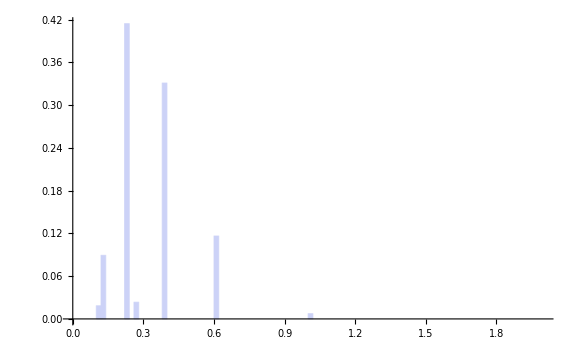
{{0.10803,85},{0.12451,411},{0.23645,1909},{0.27807,108},{0.39581,1525},{0.60998,536},{1.,34}}
{0.0184462,0.107639,0.521918,0.545356,0.876302,0.992622,1.}
{0.01648,0.01648,0.04162,0.04162,0.11774,0.21417,0.39002}
-Graphics-

```mathematica
analyzeSampleBinCombo[10.,4.,xp]
```

Here we have two pairs and 99.3% are caught using the second highest value as a threshold 98% for 9 samples). That second-highest value is still rising. It was 0.59, now it is 0.61.

#### 6 bins

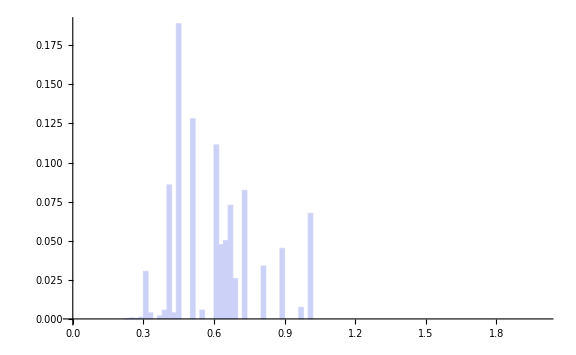
{{0.23903,1},{0.24902,3},{0.27548,2},{0.28129,2},{0.29546,3},{0.31034,120},{0.31452,20},{0.32192,4},{0.33031,14},{0.37095,9},{0.39581,26},{0.4,371},{0.41997,24},{0.43903,18},{0.44643,259},{0.44902,611},{0.51452,590},{0.55677,26},{0.6,228},{0.60998,285},{0.63903,219},{0.64643,231},{0.67548,335},{0.69546,119},{0.72451,379},{0.8,156},{0.88129,208},{0.97095,34},{1.,311}}
{0.000217014,0.000868056,0.00130208,0.00173611,0.00238715,0.0284288,0.0327691,0.0336372,0.0366753,0.0386285,0.0442708,0.124783,0.129991,0.133898,0.190104,0.3227,0.450738,0.45638,0.505859,0.567708,0.615234,0.665365,0.738064,0.763889,0.846137,0.879991,0.92513,0.932509,1.}
-Graphics-

```mathematica
analyzeSampleBinCombo[10.,6.,xp]
```

#### 8 bins

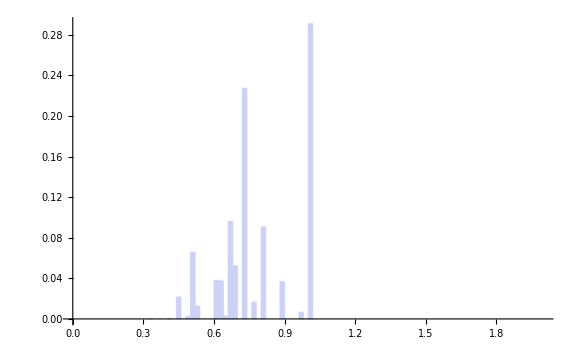
{{0.32451,1},{0.4,1},{0.44643,3},{0.44902,97},{0.49546,12},{0.51452,303},{0.52451,59},{0.6,135},{0.6058,41},{0.63903,173},{0.64643,14},{0.67548,443},{0.68129,99},{0.69546,143},{0.72192,130},{0.72451,918},{0.77095,76},{0.8,418},{0.88129,170},{0.97095,31},{1.,1341}}
{0.000217014,0.000434028,0.00108507,0.0221354,0.0247396,0.0904948,0.103299,0.132595,0.141493,0.179036,0.182075,0.278212,0.299696,0.330729,0.358941,0.55816,0.574653,0.665365,0.702257,0.708984,1.}
-Graphics-

```mathematica
analyzeSampleBinCombo[10.,8.,xp]
```

#### 9 bins

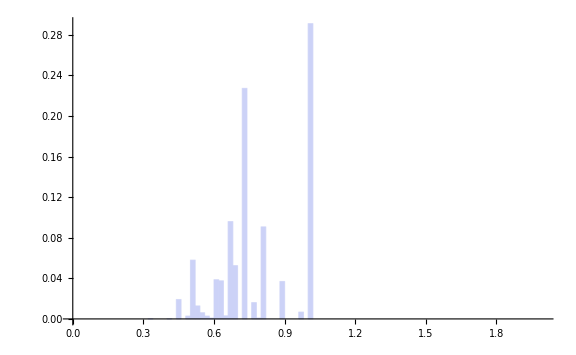
{{0.32451,1},{0.4,1},{0.44643,3},{0.44902,81},{0.45548,4},{0.48011,1},{0.48641,1},{0.49546,11},{0.51104,3},{0.51452,254},{0.51734,10},{0.52451,51},{0.53404,8},{0.55603,23},{0.55867,5},{0.56497,13},{0.58167,2},{0.5896,2},{0.6,130},{0.6058,38},{0.6126,10},{0.63903,173},{0.64643,14},{0.67548,442},{0.68129,99},{0.69546,143},{0.72192,130},{0.72451,917},{0.77095,74},{0.78641,4},{0.8,418},{0.88129,170},{0.97095,31},{1.,1341}}
{0.000217014,0.000434028,0.00108507,0.0186632,0.0195313,0.0197483,0.0199653,0.0223524,0.0230035,0.078125,0.0802951,0.0913628,0.093099,0.0980903,0.0991753,0.101997,0.102431,0.102865,0.131076,0.139323,0.141493,0.179036,0.182075,0.277995,0.299479,0.330512,0.358724,0.557726,0.573785,0.574653,0.665365,0.702257,0.708984,1.}
-Graphics-

```mathematica
analyzeSampleBinCombo[10.,9.,xp]
```

#### 10 bins

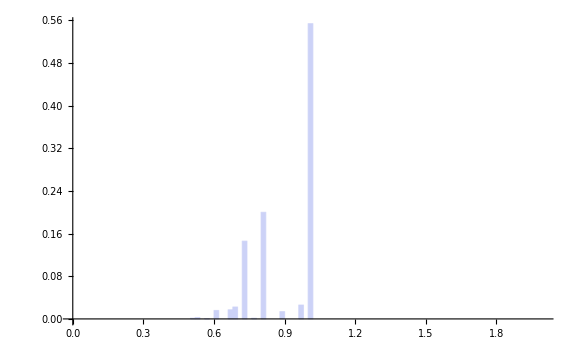
{{0.51452,6},{0.52451,12},{0.56497,1},{0.57095,1},{0.6,71},{0.6058,2},{0.67548,79},{0.68129,103},{0.72192,62},{0.72451,610},{0.77095,6},{0.8,921},{0.88129,63},{0.97095,120},{1.,2551}}
{0.00130208,0.00390625,0.00412326,0.00434028,0.0197483,0.0201823,0.0373264,0.0596788,0.0731337,0.205512,0.206814,0.406684,0.420356,0.446398,1.}
-Graphics-

```mathematica
analyzeSampleBinCombo[10.,10.,xp]
```

### Non-mic

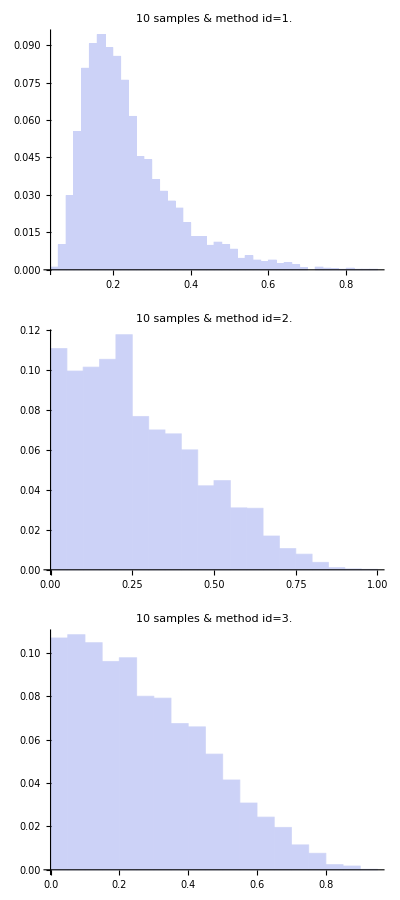

```mathematica
allNonMICHistograms[10,xp]
```

## 12 samples

### MIC

#### 4 bins

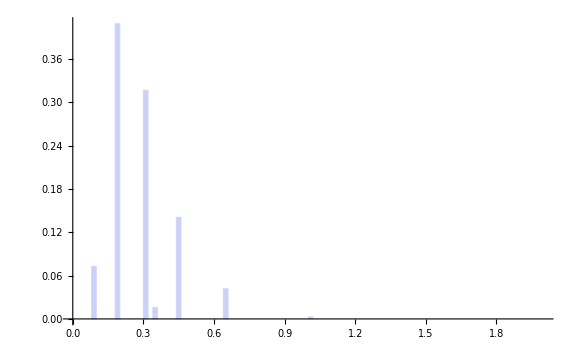
{{0.0888,69},{0.09328,266},{0.19087,1262},{0.1957,623},{0.31127,1460},{0.34997,73},{0.45914,649},{0.65485,193},{1.,13}}
{0.014974,0.0726997,0.346571,0.481771,0.798611,0.814453,0.955295,0.997179,1.}
{0.00448,0.00448,0.00483,0.00483,0.0387,0.0387,0.10917,0.19571,0.34515}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,4.,xp]
```

Here we have three pairs and 99.7% are caught using the second highest value as a threshold 99.3% for 10 samples). That second-highest value is still rising. It was 0.61, now it is 0.65.

#### 6 bins

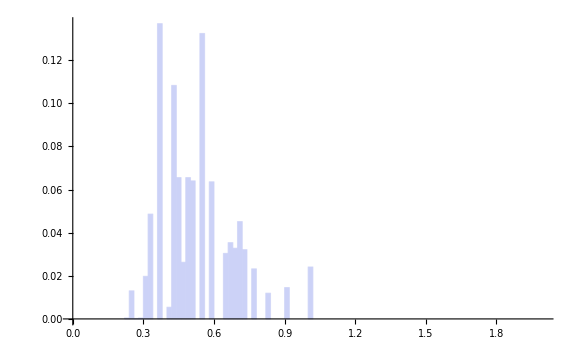
{{0.22957,2},{0.25669,60},{0.26693,1},{0.29463,2},{0.31127,34},{0.31668,57},{0.32501,48},{0.32984,13},{0.33333,163},{0.36371,182},{0.36586,43},{0.37418,38},{0.3761,134},{0.37744,234},{0.40456,25},{0.42528,499},{0.44541,18},{0.45914,284},{0.46962,121},{0.49651,302},{0.5,276},{0.50832,19},{0.54085,610},{0.59543,293},{0.65485,140},{0.66666,68},{0.67498,95},{0.69919,151},{0.70944,208},{0.72957,148},{0.77042,107},{0.83333,55},{0.91829,67},{1.,111}}
{0.000434028,0.0134549,0.0136719,0.0141059,0.0214844,0.0338542,0.0442708,0.047092,0.0824653,0.121962,0.131293,0.13954,0.16862,0.219401,0.224826,0.333116,0.337023,0.398655,0.424913,0.490451,0.550347,0.55447,0.686849,0.750434,0.780816,0.795573,0.816189,0.848958,0.894097,0.926215,0.949436,0.961372,0.975911,1.}
{0.02712,0.01024,0.01024,0.01664,0.00541002,0.00541002,0.00483,0.00349,0.00349,0.00215,0.00215,0.00192001,0.00134,0.00134,0.02072,0.02013,0.01373,0.01048,0.01048,0.00349,0.00349,0.00831997,0.03253,0.05458,0.01181,0.00831997,0.00831997,0.01025,0.01025,0.02013,0.04085,0.06291,0.08171,0.08171}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,6.,xp]
```

#### 8 bins

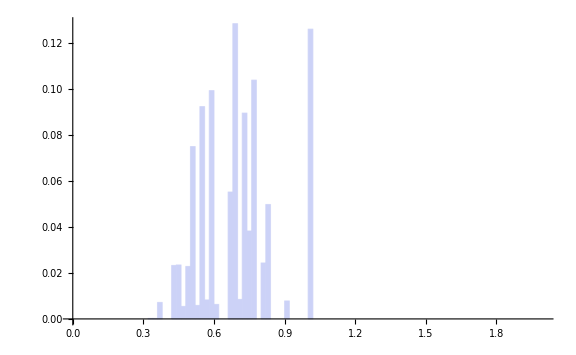
{{0.33333,1},{0.35213,1},{0.36371,15},{0.36586,8},{0.37418,2},{0.3761,2},{0.37744,6},{0.42044,5},{0.42528,78},{0.42877,18},{0.43709,6},{0.45914,108},{0.46962,25},{0.49651,105},{0.5,293},{0.50832,52},{0.52072,27},{0.54085,425},{0.5629,38},{0.59543,457},{0.60375,29},{0.66666,103},{0.67498,151},{0.68872,139},{0.69919,452},{0.70944,39},{0.72957,412},{0.75029,176},{0.77042,478},{0.81127,112},{0.83333,229},{0.91829,36},{1.,580}}
{0.000217014,0.000434028,0.00368924,0.00542535,0.00585938,0.0062934,0.00759549,0.00868056,0.0256076,0.0295139,0.030816,0.0542535,0.0596788,0.0824653,0.14605,0.157335,0.163194,0.255425,0.263672,0.362847,0.369141,0.391493,0.424262,0.454427,0.552517,0.560981,0.650391,0.688585,0.792318,0.816623,0.866319,0.874132,1.}
{0.0188,0.01158,0.00215,0.00215,0.00192001,0.00134,0.00134,0.00484002,0.00349,0.00349,0.00832,0.01048,0.01048,0.00349,0.00349,0.00831997,0.0124,0.02013,0.02205,0.00831997,0.00831997,0.00831997,0.00831997,0.01047,0.01025,0.01025,0.02013,0.02013,0.02013,0.02206,0.02206,0.08171,0.08171}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,8.,xp]
```

#### 9 bins

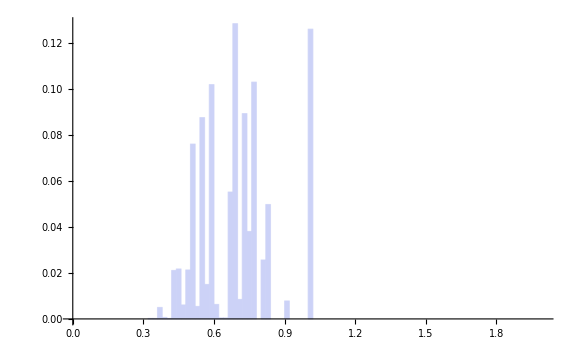
{{0.33333,1},{0.35213,1},{0.36371,15},{0.36586,3},{0.36907,3},{0.37418,1},{0.37744,1},{0.38959,1},{0.39484,2},{0.40876,1},{0.42044,5},{0.42528,66},{0.42877,15},{0.42928,5},{0.43453,1},{0.43709,5},{0.45505,6},{0.45914,94},{0.46677,5},{0.46962,23},{0.49254,5},{0.49474,2},{0.49651,91},{0.5,298},{0.50832,52},{0.52072,25},{0.54085,393},{0.55496,10},{0.5629,33},{0.56546,2},{0.57938,34},{0.59543,452},{0.5999,17},{0.60375,29},{0.63959,2},{0.65876,2},{0.66666,103},{0.67498,151},{0.68872,139},{0.69919,452},{0.70944,39},{0.72957,411},{0.75029,175},{0.77042,474},{0.81021,6},{0.81127,112},{0.83333,229},{0.91829,36},{1.,580}}
{0.000217014,0.000434028,0.00368924,0.00434028,0.00499132,0.00520833,0.00542535,0.00564236,0.00607639,0.0062934,0.00737847,0.0217014,0.0249566,0.0260417,0.0262587,0.0273438,0.0286458,0.0490451,0.0501302,0.0551215,0.0562066,0.0566406,0.0763889,0.141059,0.152344,0.157769,0.243056,0.245226,0.252387,0.252821,0.2602,0.35829,0.361979,0.368273,0.368707,0.369141,0.391493,0.424262,0.454427,0.552517,0.560981,0.650174,0.688151,0.791016,0.792318,0.816623,0.866319,0.874132,1.}
{0.0188,0.01158,0.00215,0.00215,0.00321001,0.00326002,0.00326002,0.00525001,0.00525001,0.01168,0.00484002,0.00349,0.000510007,0.000510007,0.00256002,0.00256002,0.00409001,0.00409001,0.00285,0.00285,0.00220001,0.00176999,0.00176999,0.00349,0.00831997,0.0124,0.01411,0.00793999,0.00256002,0.00256002,0.0139199,0.00446999,0.00384998,0.00384998,0.01917,0.0079,0.0079,0.00831997,0.01047,0.01025,0.01025,0.02013,0.02013,0.02013,0.00106001,0.00106001,0.02206,0.08171,0.08171}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,9.,xp]
```

#### 10 bins

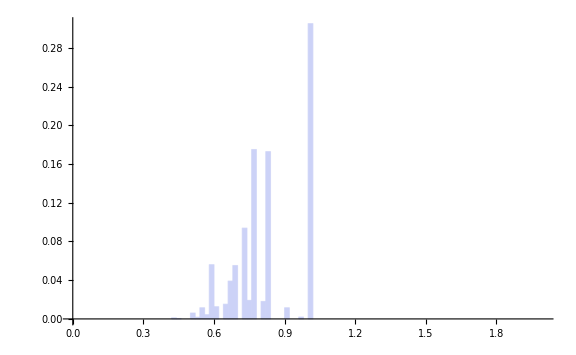
{{0.42528,2},{0.42877,1},{0.43709,2},{0.45914,2},{0.5,28},{0.52205,4},{0.53253,4},{0.54085,52},{0.55496,1},{0.5629,16},{0.57938,4},{0.5817,14},{0.58362,10},{0.58496,2},{0.59543,230},{0.5999,2},{0.60375,58},{0.64461,44},{0.64653,1},{0.65002,23},{0.65876,2},{0.66666,180},{0.68872,64},{0.69919,190},{0.72957,432},{0.75029,50},{0.75162,38},{0.77042,806},{0.81127,60},{0.8132,23},{0.83333,796},{0.91829,53},{0.97986,9},{1.,1405}}
{0.000434028,0.000651042,0.00108507,0.0015191,0.00759549,0.00846354,0.0093316,0.0206163,0.0208333,0.0243056,0.0251736,0.0282118,0.0303819,0.030816,0.0807292,0.0811632,0.09375,0.103299,0.103516,0.108507,0.108941,0.148003,0.161892,0.203125,0.296875,0.307726,0.315972,0.490885,0.503906,0.508898,0.681641,0.693142,0.695095,1.}
{0.00349,0.00349,0.00832,0.02205,0.02205,0.01048,0.00831997,0.00831997,0.00793999,0.00793999,0.00232005,0.00191998,0.00133997,0.00133997,0.00446999,0.00384998,0.00384998,0.00191998,0.00191998,0.00349003,0.0079,0.0079,0.01047,0.01047,0.02072,0.00133002,0.00133002,0.0188,0.00193,0.00193,0.02013,0.06157,0.02014,0.02014}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,10.,xp]
```

#### 12 bins

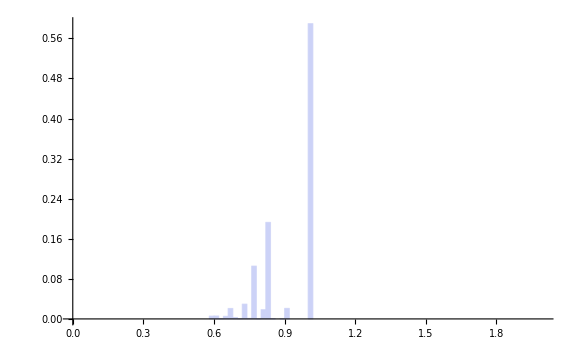
{{0.58496,2},{0.59543,21},{0.5999,3},{0.60375,27},{0.63092,1},{0.63739,1},{0.64461,20},{0.65002,4},{0.66536,1},{0.66666,95},{0.68872,8},{0.69114,1},{0.69919,4},{0.7103,2},{0.72957,136},{0.75029,2},{0.75162,3},{0.77042,482},{0.77577,4},{0.78969,1},{0.81021,3},{0.81127,8},{0.8132,74},{0.82938,2},{0.83333,883},{0.83598,3},{0.85515,3},{0.89484,1},{0.91829,97},{1.,2716}}
{0.000434028,0.00499132,0.00564236,0.0115017,0.0117188,0.0119358,0.016276,0.0171441,0.0173611,0.0379774,0.0397135,0.0399306,0.0407986,0.0412326,0.0707465,0.0711806,0.0718316,0.176432,0.1773,0.177517,0.178168,0.179905,0.195964,0.196398,0.388021,0.388672,0.389323,0.38954,0.41059,1.}
{0.01047,0.00446999,0.00384998,0.00384998,0.00647002,0.00647002,0.00541002,0.00541002,0.00130004,0.00130004,0.00242001,0.00242001,0.00805002,0.01111,0.0192699,0.00133002,0.00133002,0.00534999,0.00534999,0.01392,0.00106001,0.00106001,0.00193,0.00395,0.00265002,0.00265002,0.01917,0.02345,0.02345,0.08171}
-Graphics-

```mathematica
analyzeSampleBinCombo[12.,12.,xp]
```

### Non-mic

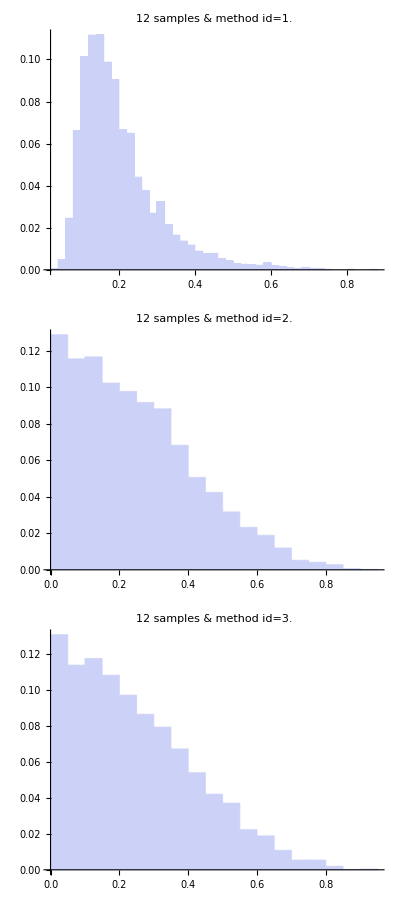

```mathematica
allNonMICHistograms[12,xp]
```

## 14 samples

### MIC

#### 4 bins

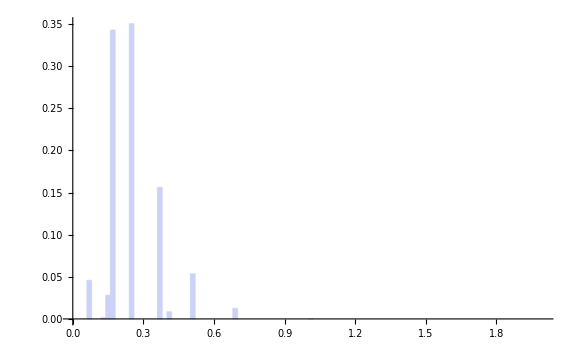
{{0.07539,211},{0.13687,7},{0.15183,130},{0.16011,1580},{0.25698,1178},{0.25783,437},{0.3705,720},{0.40832,39},{0.50872,247},{0.68939,58},{1.,1}}
{0.0457899,0.047309,0.0755208,0.418403,0.674045,0.76888,0.92513,0.933594,0.987196,0.999783,1.}
{0.06148,0.01496,0.00827999,0.00827999,0.000849992,0.000849992,0.03782,0.03782,0.1004,0.18067,0.31061}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,4.,xp]
```

Here we have only two pairs and 99.97% are caught using the second highest value as a threshold 99.7% for 12 samples). That second-highest value is still rising. It was 0.65, now it is 0.68.

There are now 11 possible values and in general, the values seem to be assuming a nice single-peaked distribution, a bit skewed to the left.

#### 6 bins

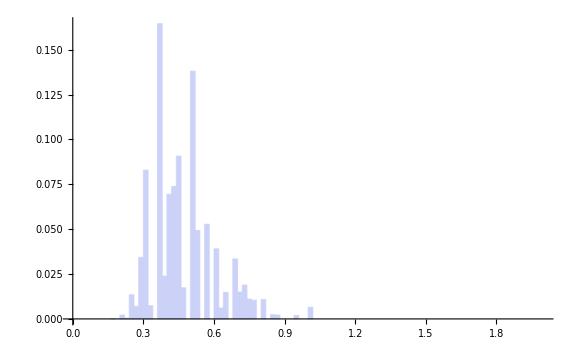
{{0.17787,1},{0.21897,10},{0.23063,2},{0.2449,1},{0.24674,2},{0.24955,1},{0.25698,3},{0.25783,23},{0.25852,12},{0.25967,20},{0.2668,5},{0.27559,21},{0.27858,6},{0.28455,8},{0.28571,130},{0.28985,4},{0.29169,16},{0.30461,10},{0.30595,72},{0.30646,238},{0.3078,4},{0.31359,58},{0.32786,25},{0.33963,9},{0.36172,19},{0.36287,295},{0.3705,129},{0.37166,48},{0.37349,72},{0.37465,195},{0.38062,36},{0.39355,23},{0.3954,51},{0.40282,63},{0.40666,48},{0.40966,209},{0.42462,37},{0.42558,28},{0.42857,211},{0.4357,64},{0.44168,25},{0.44633,44},{0.45066,29},{0.4546,320},{0.46956,45},{0.47236,35},{0.50738,230},{0.50872,217},{0.51037,82},{0.5178,107},{0.52464,75},{0.53641,152},{0.5613,4},{0.56843,151},{0.57142,88},{0.60528,58},{0.60644,122},{0.63846,28},{0.65323,68},{0.68245,55},{0.68939,99},{0.70416,37},{0.71428,32},{0.72141,54},{0.72739,33},{0.74216,43},{0.75343,8},{0.7682,48},{0.80322,50},{0.85714,11},{0.86312,10},{0.94028,9},{1.,30}}
{0.000217014,0.00238715,0.00282118,0.00303819,0.00347222,0.00368924,0.00434028,0.0093316,0.0119358,0.016276,0.0173611,0.0219184,0.0232205,0.0249566,0.0531684,0.0540365,0.0575087,0.0596788,0.0753038,0.126953,0.127821,0.140408,0.145833,0.147786,0.15191,0.215929,0.243924,0.25434,0.269965,0.312283,0.320095,0.325087,0.336155,0.349826,0.360243,0.405599,0.413628,0.419705,0.465495,0.479384,0.484809,0.494358,0.500651,0.570095,0.579861,0.587457,0.63737,0.684462,0.702257,0.725477,0.741753,0.77474,0.775608,0.808377,0.827474,0.840061,0.866536,0.872613,0.88737,0.899306,0.92079,0.928819,0.935764,0.947483,0.954644,0.963976,0.965712,0.976128,0.986979,0.989366,0.991536,0.99349,1.}
{0.0411,0.01166,0.01166,0.00184,0.00184,0.00281,0.000849992,0.000690013,0.000690013,0.00114998,0.00713,0.00299001,0.00299001,0.00116,0.00116,0.00184,0.00184,0.00133997,0.000510007,0.000510007,0.00134,0.00579,0.01177,0.01177,0.00115001,0.00115001,0.00116,0.00116,0.00116,0.00116,0.00597,0.00184998,0.00184998,0.00384,0.00300002,0.00300002,0.000959992,0.000959992,0.00299001,0.00598001,0.00465,0.00432998,0.00394002,0.00394002,0.00279999,0.00279999,0.00133997,0.00133997,0.00165004,0.00684005,0.00684005,0.01177,0.00713003,0.00299001,0.00299001,0.00116003,0.00116003,0.01477,0.01477,0.00694001,0.00694001,0.01012,0.00712997,0.00598001,0.00598001,0.01127,0.01127,0.01477,0.03502,0.00598001,0.00598001,0.05972,0.05972}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,6.,xp]
```

#### 8 bins

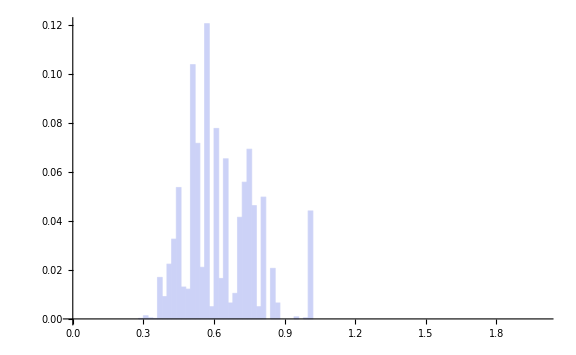
{{0.28571,1},{0.30646,4},{0.3106,1},{0.31175,1},{0.32102,1},{0.33664,1},{0.35604,1},{0.36287,23},{0.36452,5},{0.37166,9},{0.37349,2},{0.37465,39},{0.38062,7},{0.39355,6},{0.39489,9},{0.3954,14},{0.39953,6},{0.40966,103},{0.42143,15},{0.42277,14},{0.42462,3},{0.42558,1},{0.42857,95},{0.43454,12},{0.4357,10},{0.44283,3},{0.4546,206},{0.45645,38},{0.46358,30},{0.46772,5},{0.46956,23},{0.47669,2},{0.48249,31},{0.48433,20},{0.48962,5},{0.50273,2},{0.50738,224},{0.51037,164},{0.51171,44},{0.5175,3},{0.5178,41},{0.52164,15},{0.52464,67},{0.53641,248},{0.54539,52},{0.55665,45},{0.5613,34},{0.56843,228},{0.57142,290},{0.57856,3},{0.59167,11},{0.59931,12},{0.60644,358},{0.62534,23},{0.63132,39},{0.63846,14},{0.65323,273},{0.65457,28},{0.66036,12},{0.66634,18},{0.68245,33},{0.69951,15},{0.70416,96},{0.70849,14},{0.71428,81},{0.72141,256},{0.72739,1},{0.74216,215},{0.7435,34},{0.74959,51},{0.75343,19},{0.7682,213},{0.78845,23},{0.80322,229},{0.85714,95},{0.86312,30},{0.94028,4},{0.98522,2},{1.,203}}
{0.000217014,0.00108507,0.00130208,0.0015191,0.00173611,0.00195313,0.00217014,0.00716146,0.00824653,0.0101997,0.0106337,0.0190972,0.0206163,0.0219184,0.0238715,0.0269097,0.0282118,0.0505642,0.0538194,0.0568576,0.0575087,0.0577257,0.078342,0.0809462,0.0831163,0.0837674,0.128472,0.136719,0.143229,0.144314,0.149306,0.14974,0.156467,0.160807,0.161892,0.162326,0.210938,0.246528,0.256076,0.256727,0.265625,0.26888,0.28342,0.33724,0.348524,0.35829,0.365668,0.415148,0.478082,0.478733,0.48112,0.483724,0.561415,0.566406,0.57487,0.577908,0.637153,0.643229,0.645833,0.64974,0.656901,0.660156,0.68099,0.684028,0.701606,0.757161,0.757378,0.804036,0.811415,0.822483,0.826606,0.87283,0.877821,0.927517,0.948134,0.954644,0.955512,0.955946,1.}
{0.02075,0.00414002,0.00114998,0.00114998,0.00927001,0.01562,0.00683001,0.00165001,0.00165001,0.00183001,0.00116,0.00116,0.00597,0.00134,0.000509977,0.000509977,0.00413001,0.01013,0.00134,0.00134,0.000959992,0.000959992,0.00299001,0.00116,0.00116,0.00713,0.00184998,0.00184998,0.00413999,0.00184,0.00184,0.00580001,0.00184,0.00184,0.00529,0.00465,0.00299001,0.00133997,0.00133997,0.00029999,0.00029999,0.00300002,0.00300002,0.00898004,0.00898004,0.00465,0.00465,0.00299001,0.00299001,0.00713998,0.00764,0.00713003,0.00713003,0.00598001,0.00598001,0.00713998,0.00133997,0.00133997,0.00579,0.00598001,0.01611,0.00465,0.00433004,0.00433004,0.00579,0.00598001,0.00598001,0.00133997,0.00133997,0.00384003,0.00384003,0.01477,0.01477,0.01477,0.00598001,0.00598001,0.04494,0.01478,0.01478}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,8.,xp]
```

#### 9 bins

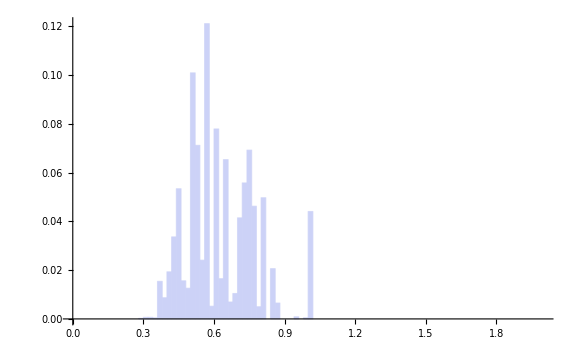
{{0.28571,1},{0.30646,1},{0.3106,1},{0.31175,1},{0.32285,1},{0.32578,2},{0.35604,1},{0.35791,1},{0.36287,22},{0.3643,2},{0.36452,5},{0.37166,8},{0.37465,34},{0.38062,4},{0.38189,3},{0.39355,5},{0.39489,9},{0.3954,13},{0.39953,6},{0.40966,88},{0.41298,1},{0.42041,2},{0.42143,14},{0.42277,14},{0.42462,1},{0.42857,90},{0.43234,1},{0.4335,5},{0.43454,11},{0.4357,10},{0.43612,3},{0.438,4},{0.44283,2},{0.447,6},{0.45254,1},{0.45443,1},{0.4546,198},{0.45645,37},{0.45893,1},{0.4601,3},{0.46358,27},{0.46564,1},{0.46752,1},{0.46772,5},{0.4691,5},{0.46956,22},{0.47086,3},{0.47202,2},{0.47652,1},{0.47669,2},{0.48249,31},{0.48433,20},{0.48845,2},{0.48962,5},{0.50273,2},{0.50416,3},{0.50738,223},{0.51037,160},{0.51171,40},{0.5175,3},{0.5178,34},{0.52164,15},{0.52464,66},{0.52697,3},{0.52814,3},{0.53264,1},{0.53641,240},{0.54268,1},{0.54456,11},{0.54539,51},{0.54906,1},{0.55665,45},{0.55766,2},{0.56027,1},{0.5613,33},{0.56843,225},{0.57116,4},{0.57142,289},{0.5767,3},{0.57856,3},{0.58425,1},{0.59167,11},{0.59931,12},{0.60068,2},{0.60644,357},{0.62534,23},{0.63132,39},{0.63846,14},{0.65323,273},{0.65457,28},{0.66036,12},{0.66634,18},{0.66988,2},{0.68245,33},{0.69951,15},{0.70416,96},{0.70849,14},{0.71428,81},{0.72141,256},{0.72739,1},{0.74216,215},{0.7435,34},{0.74959,51},{0.75343,19},{0.7682,213},{0.78845,23},{0.80322,229},{0.85714,95},{0.86312,30},{0.94028,4},{0.98522,2},{1.,203}}
{0.000217014,0.000434028,0.000651042,0.000868056,0.00108507,0.0015191,0.00173611,0.00195313,0.00672743,0.00716146,0.00824653,0.00998264,0.0173611,0.0182292,0.0188802,0.0199653,0.0219184,0.0247396,0.0260417,0.0451389,0.0453559,0.0457899,0.0488281,0.0518663,0.0520833,0.0716146,0.0718316,0.0729167,0.0753038,0.077474,0.078125,0.0789931,0.0794271,0.0807292,0.0809462,0.0811632,0.124132,0.132161,0.132378,0.13303,0.138889,0.139106,0.139323,0.140408,0.141493,0.146267,0.146918,0.147352,0.147569,0.148003,0.154731,0.159071,0.159505,0.16059,0.161024,0.161675,0.210069,0.244792,0.253472,0.254123,0.261502,0.264757,0.27908,0.279731,0.280382,0.280599,0.332682,0.332899,0.335286,0.346354,0.346571,0.356337,0.356771,0.356988,0.364149,0.412977,0.413845,0.476563,0.477214,0.477865,0.478082,0.480469,0.483073,0.483507,0.560981,0.565972,0.574436,0.577474,0.636719,0.642795,0.645399,0.649306,0.64974,0.656901,0.660156,0.68099,0.684028,0.701606,0.757161,0.757378,0.804036,0.811415,0.822483,0.826606,0.87283,0.877821,0.927517,0.948134,0.954644,0.955512,0.955946,1.}
{0.02075,0.00414002,0.00114998,0.00114998,0.00293002,0.00293002,0.00187001,0.00187001,0.00143,0.000220001,0.000220001,0.00299001,0.00299001,0.00127,0.00127,0.00134,0.000509977,0.000509977,0.00413001,0.00331998,0.00331998,0.00101998,0.00101998,0.00134,0.00185001,0.00376999,0.00116,0.00104001,0.00104001,0.000420004,0.000420004,0.00187999,0.00417,0.00417,0.00189,0.000169992,0.000169992,0.00184998,0.00117001,0.00117001,0.00206,0.00187999,0.000200003,0.000200003,0.000459999,0.000459999,0.00116,0.00116,0.000169992,0.000169992,0.00184,0.00184,0.00117001,0.00117001,0.00142998,0.00142998,0.00299001,0.00133997,0.00133997,0.00029999,0.00029999,0.00300002,0.00233001,0.00116998,0.00116998,0.00376999,0.00376999,0.00187999,0.000829995,0.000829995,0.00366998,0.00101,0.00101,0.00102997,0.00102997,0.00273001,0.000259995,0.000259995,0.00186002,0.00186002,0.00568998,0.00742,0.00137001,0.00137001,0.00576001,0.00598001,0.00598001,0.00713998,0.00133997,0.00133997,0.00579,0.00353998,0.00353998,0.01257,0.00465,0.00433004,0.00433004,0.00579,0.00598001,0.00598001,0.00133997,0.00133997,0.00384003,0.00384003,0.01477,0.01477,0.01477,0.00598001,0.00598001,0.04494,0.01478,0.01478}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,9.,xp]
```

#### 10 bins

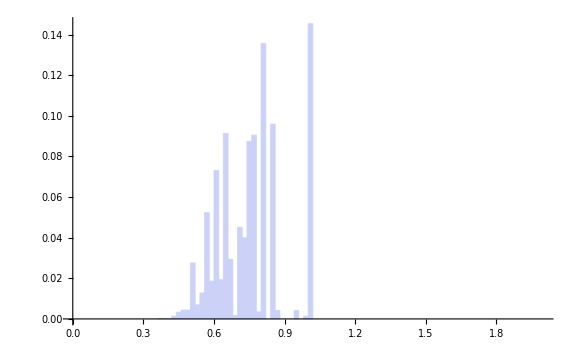
{{0.37465,1},{0.39489,1},{0.40966,1},{0.42857,5},{0.43454,1},{0.4546,10},{0.45645,5},{0.46358,7},{0.4691,1},{0.46956,12},{0.48249,18},{0.48433,2},{0.50738,81},{0.51037,29},{0.51171,5},{0.5175,10},{0.5178,2},{0.52164,2},{0.53641,30},{0.54539,29},{0.54673,17},{0.55281,9},{0.55665,2},{0.55766,2},{0.56843,55},{0.57142,166},{0.57856,20},{0.59167,38},{0.59931,48},{0.60065,12},{0.60644,325},{0.62534,82},{0.63132,7},{0.64559,5},{0.65323,409},{0.65457,7},{0.66036,47},{0.66634,87},{0.66988,1},{0.68245,7},{0.69951,1},{0.70849,2},{0.71428,206},{0.72026,18},{0.72141,166},{0.74216,291},{0.7435,64},{0.74959,48},{0.7682,417},{0.78845,16},{0.80322,625},{0.85714,442},{0.86312,19},{0.94028,19},{0.98522,6},{1.,670}}
{0.000217014,0.000434028,0.000651042,0.00173611,0.00195313,0.00412326,0.00520833,0.00672743,0.00694444,0.00954861,0.0134549,0.0138889,0.031467,0.0377604,0.0388455,0.0410156,0.0414497,0.0418837,0.0483941,0.0546875,0.0583767,0.0603299,0.0607639,0.0611979,0.0731337,0.109158,0.113498,0.121745,0.132161,0.134766,0.205295,0.22309,0.224609,0.225694,0.314453,0.315972,0.326172,0.345052,0.345269,0.346788,0.347005,0.347439,0.392144,0.39605,0.432075,0.495226,0.509115,0.519531,0.610026,0.613498,0.749132,0.845052,0.849175,0.853299,0.854601,1.}
{0.02024,0.01477,0.01477,0.00597,0.00597,0.00184998,0.00184998,0.00551999,0.000459999,0.000459999,0.00184,0.00184,0.00299001,0.00133997,0.00133997,0.00029999,0.00029999,0.00384003,0.00898004,0.00133997,0.00133997,0.00383997,0.00101,0.00101,0.00299001,0.00299001,0.00713998,0.00764,0.00134003,0.00134003,0.00579,0.00598001,0.00598001,0.00764,0.00133997,0.00133997,0.00579,0.00353998,0.00353998,0.01257,0.00898004,0.00579,0.00579,0.00114995,0.00114995,0.00133997,0.00133997,0.00608999,0.01861,0.01477,0.01477,0.00598001,0.00598001,0.04494,0.01478,0.01478}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,10.,xp]
```

#### 12 bins

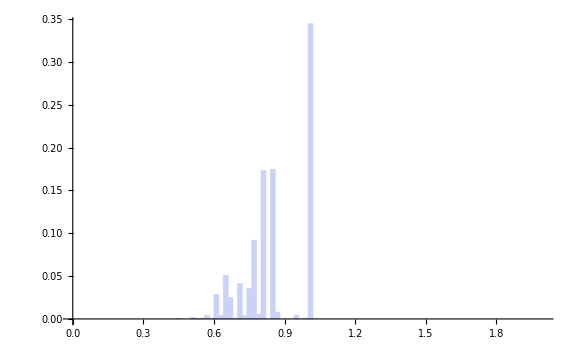
{{0.45645,1},{0.45779,1},{0.50738,2},{0.51037,1},{0.51054,1},{0.5175,5},{0.52348,1},{0.55281,3},{0.56843,1},{0.57142,16},{0.5774,2},{0.59167,1},{0.59931,2},{0.60065,1},{0.60644,107},{0.60673,22},{0.61377,2},{0.6216,1},{0.62277,2},{0.62534,14},{0.6302,1},{0.63281,1},{0.64559,9},{0.65112,1},{0.65229,2},{0.65323,217},{0.65457,4},{0.65679,1},{0.66036,78},{0.66634,36},{0.67322,1},{0.69951,2},{0.71428,190},{0.72026,10},{0.72141,7},{0.74216,134},{0.74242,1},{0.7435,23},{0.74959,7},{0.7682,423},{0.78845,14},{0.79548,1},{0.79742,11},{0.80322,796},{0.81946,1},{0.84237,20},{0.84898,1},{0.85714,782},{0.85798,1},{0.86312,36},{0.94028,19},{0.98522,4},{1.,1588}}
{0.000217014,0.000434028,0.000868056,0.00108507,0.00130208,0.00238715,0.00260417,0.00325521,0.00347222,0.00694444,0.00737847,0.00759549,0.00802951,0.00824653,0.031467,0.0362413,0.0366753,0.0368924,0.0373264,0.0403646,0.0405816,0.0407986,0.0427517,0.0429688,0.0434028,0.0904948,0.0913628,0.0915799,0.108507,0.116319,0.116536,0.11697,0.158203,0.160373,0.161892,0.190972,0.191189,0.196181,0.1977,0.289497,0.292535,0.292752,0.295139,0.467882,0.468099,0.472439,0.472656,0.642361,0.642578,0.650391,0.654514,0.655382,1.}
{0.00134,0.00134,0.00299001,0.000169992,0.000169992,0.00598001,0.00598001,0.01562,0.00299001,0.00299001,0.00598001,0.00764,0.00134003,0.00134003,0.000289977,0.000289977,0.00704002,0.00117004,0.00117004,0.00256997,0.00260997,0.00260997,0.00553,0.00116998,0.000940025,0.000940025,0.00133997,0.00222003,0.00356996,0.00598001,0.00687999,0.01477,0.00598001,0.00114995,0.00114995,0.000259995,0.000259995,0.00107998,0.00608999,0.01861,0.00703001,0.00194001,0.00194001,0.00579995,0.01624,0.00661004,0.00661004,0.000840008,0.000840008,0.00514001,0.04494,0.01478,0.01478}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,12.,xp]
```

#### 14 bins

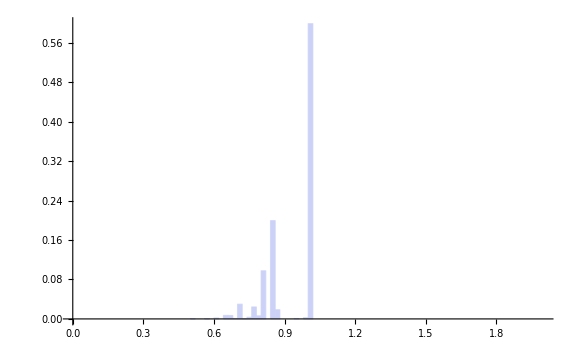
{{0.5175,1},{0.57142,1},{0.5774,1},{0.60644,6},{0.60673,3},{0.64559,1},{0.65323,32},{0.66036,31},{0.66634,1},{0.69951,4},{0.71428,138},{0.72026,2},{0.74216,12},{0.7435,3},{0.74959,1},{0.7682,112},{0.79742,29},{0.80322,450},{0.85714,919},{0.86312,86},{0.94028,4},{0.98522,11},{1.,2760}}
{0.000217014,0.000434028,0.000651042,0.00195313,0.00260417,0.00282118,0.00976563,0.0164931,0.0167101,0.0175781,0.047526,0.0479601,0.0505642,0.0512153,0.0514323,0.0757378,0.0820313,0.179688,0.379123,0.397786,0.398655,0.401042,1.}
{0.05392,0.00598001,0.00598001,0.000289977,0.000289977,0.00764,0.00712997,0.00598001,0.00598001,0.01477,0.00598001,0.00598001,0.00133997,0.00133997,0.00608999,0.01861,0.00579995,0.00579995,0.00598001,0.00598001,0.04494,0.01478,0.01478}
-Graphics-

```mathematica
analyzeSampleBinCombo[14.,14.,xp]
```

### Non-mic

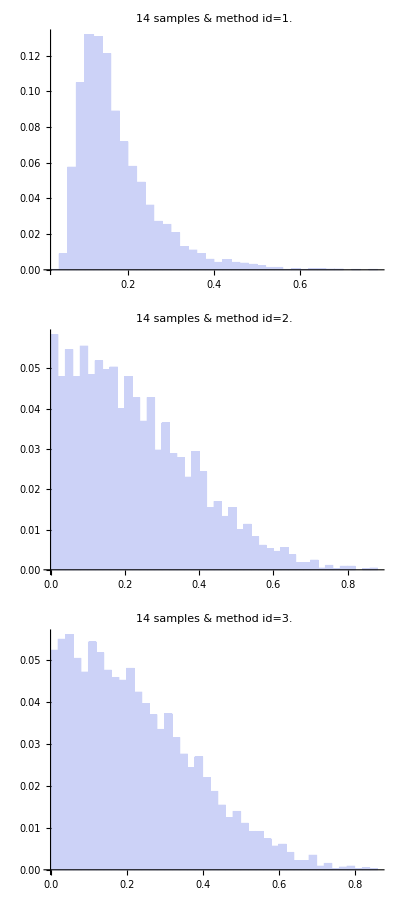

```mathematica
allNonMICHistograms[14,xp]
```

## 19 samples

### MIC

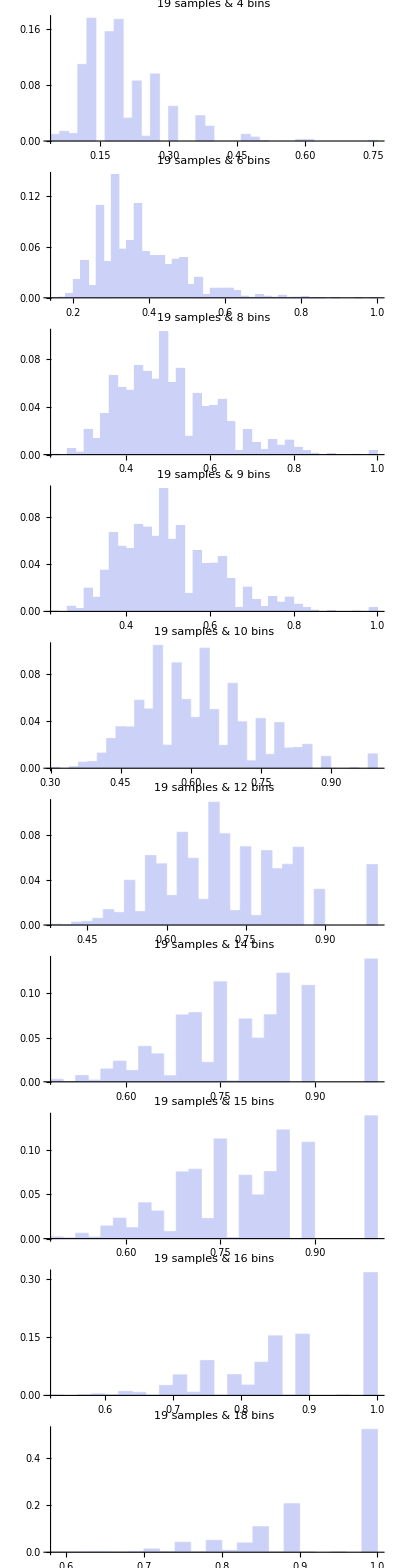

```mathematica
allHistograms[19,xp]
```

### Non-mic

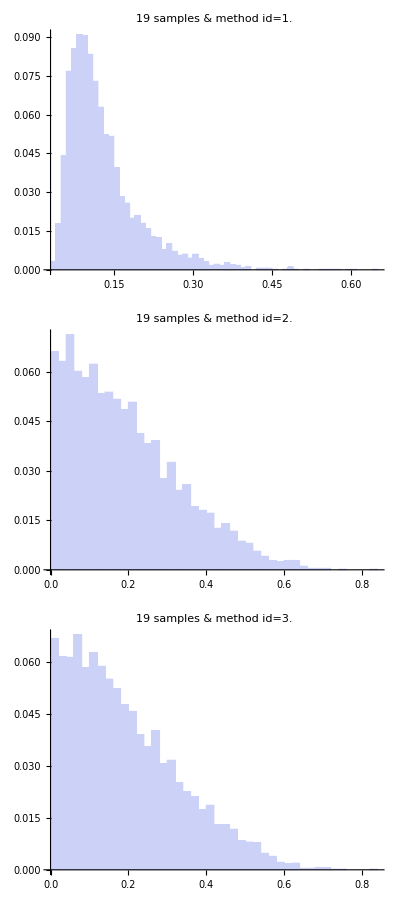

```mathematica
allNonMICHistograms[19,xp]
```

## 30 samples

### MIC

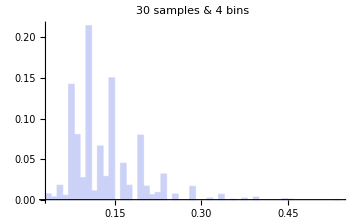
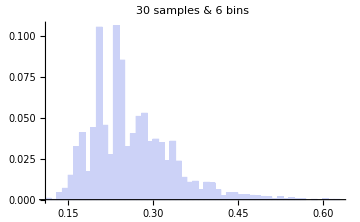
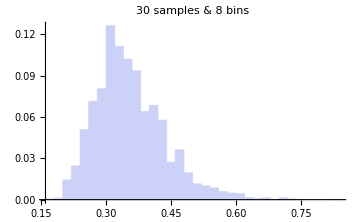
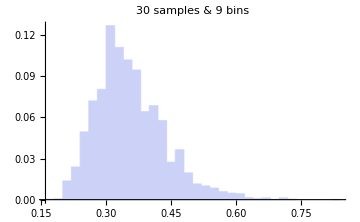
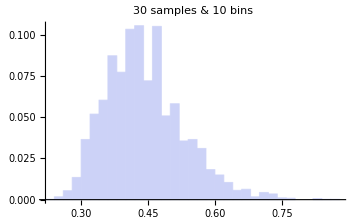
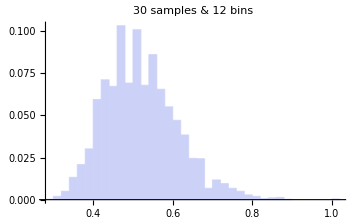
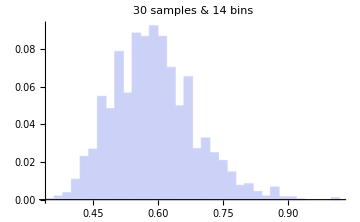
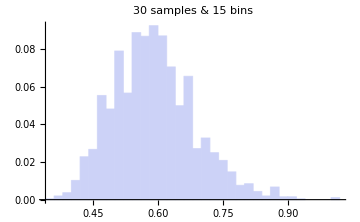

```mathematica
allHistograms[30,xp]
```

### Non-mic

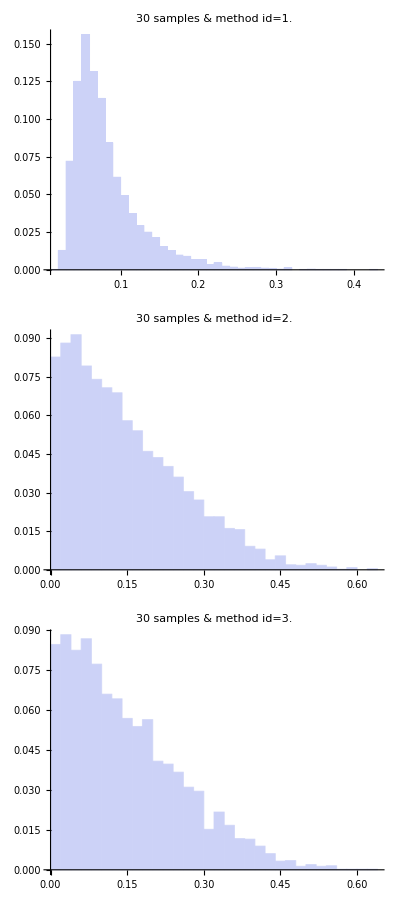

```mathematica
allNonMICHistograms[30,xp]
```

## 60 samples

### MIC

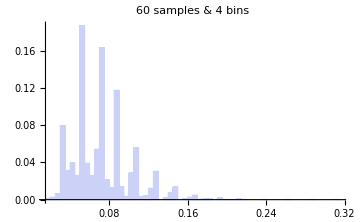
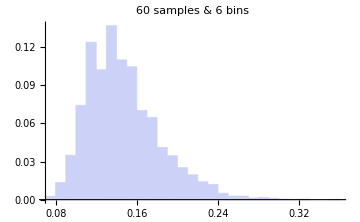
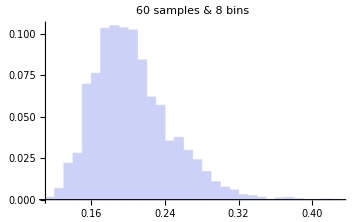
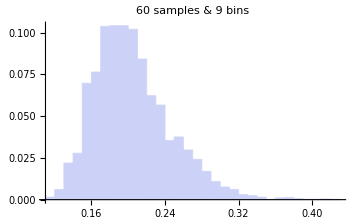
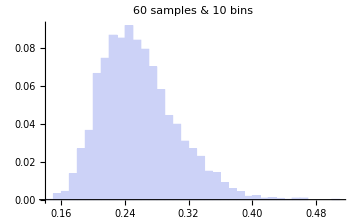
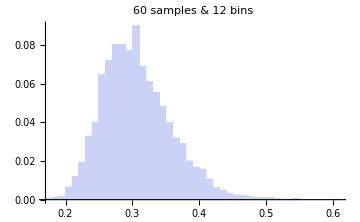
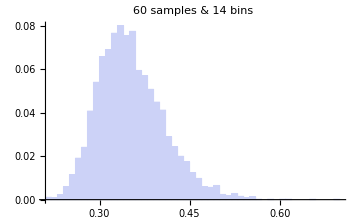
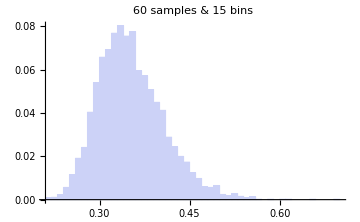

```mathematica
allHistograms[60,xp]
```

### Non-mic

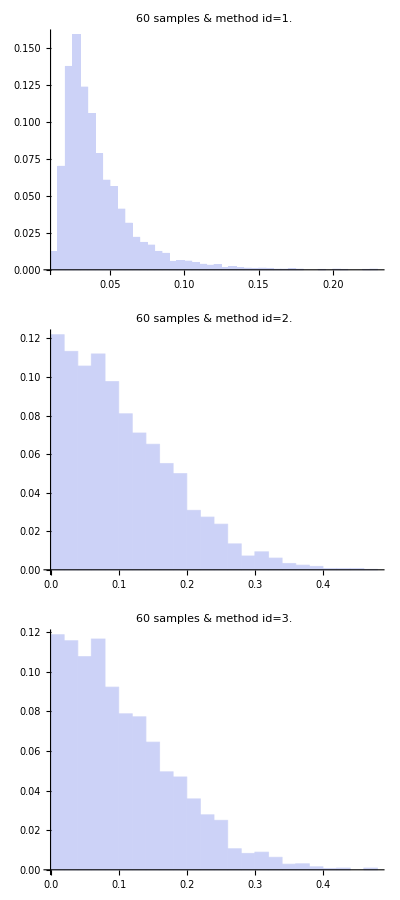

```mathematica
allNonMICHistograms[60,xp]
```

## 100 samples

### MIC

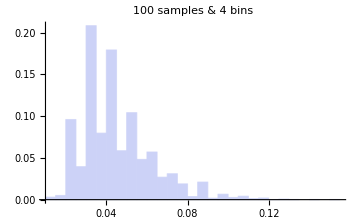
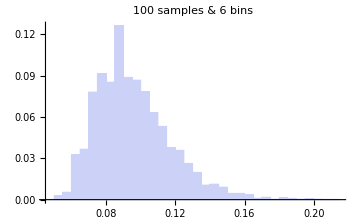
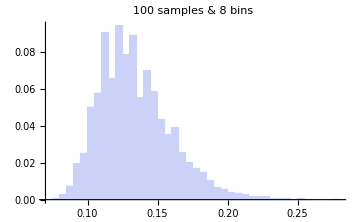
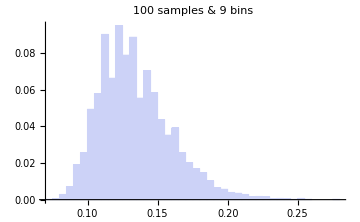
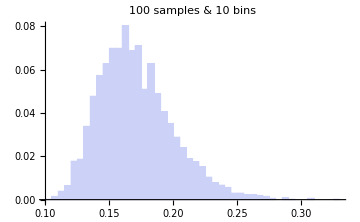
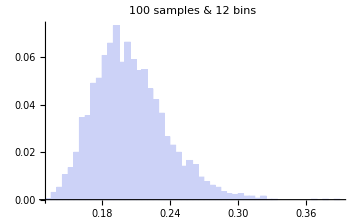
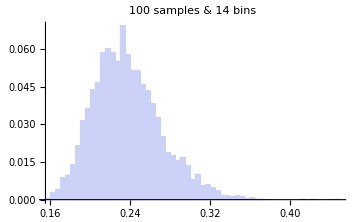
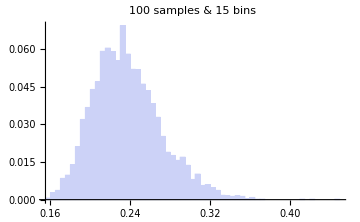
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
allHistograms[100,xp]
```

### Non-mic

```mathematica
allNonMICHistograms[100,xp]
```

-Graphics-
-Graphics-
-Graphics-